```mathematica
er=(1+2 En h^2 (1+(-15/2+5/2 v)En/c^2+((-6+v)/(c^2 h^2))))^(1/2)
et=(1+2 En h^2 (1+(17/2-7/2 v)En/c^2+((2-2v)/(c^2 h^2))))^(1/2)
ep=(1+2 En h^2 (1+(-15/2+1/2 v)En/c^2+((-6)/(c^2 h^2))))^(1/2)
```

√(1+2 En h^2 (1+(-6+v)/(c^2 h^2)+(En (-15/2+(5 v)/2))/c^2))

√(1+2 En h^2 (1+(En (17/2-(7 v)/2))/c^2+(2-2 v)/(c^2 h^2)))

√(1+2 En h^2 (1-6/(c^2 h^2)+(En (-15/2+v/2))/c^2))

```mathematica
Series[et/er,{c,Infinity,2}]//Normal
Series[et/ep,{c,Infinity,2}]//Normal
Series[er/ep,{c,Infinity,2}]//Normal
```

1+(8 En-3 En v)/c^2

1-(2 (-4 En+En v))/c^2

1+(En v)/c^2

```mathematica
ER=Series[er,{c,Infinity,2}]//Normal
ET=Series[et,{c,Infinity,2}]//Normal
EP=Series[ep,{c,Infinity,2}]//Normal
```

√(1+2 En h^2)+(En (-12-15 En h^2+2 v+5 En h^2 v))/(2 c^2 √(1+2 En h^2))

√(1+2 En h^2)-(En (-4-17 En h^2+4 v+7 En h^2 v))/(2 c^2 √(1+2 En h^2))

√(1+2 En h^2)+(En (-12-15 En h^2+En h^2 v))/(2 c^2 √(1+2 En h^2))

```mathematica
A=√(1+2 En h^2)
B=(En (-12-15 En h^2+2 v+5 En h^2 v))/(2 √(1+2 En h^2))
```

√(1+2 En h^2)

(En (-12-15 En h^2+2 v+5 En h^2 v))/(2 √(1+2 En h^2))

```mathematica
FullSimplify[EP-(A+1/c^2 (B+L-A^2 L))]
```

(En (2 h^2 L-√(1+2 En h^2) v))/c^2

```mathematica
Solve[(En (2 h^2 L-√(1+2 En h^2) v))/c^2==0,L][[1,1]]
```

L→(√(1+2 En h^2) v)/(2 h^2)

```mathematica
mr=A+B/c^2
mp=(A+1/c^2 (B+L-A^2 L))

FullSimplify[Series[Sqrt[((mr+1)/(mr-1))((mp-1)/(mp+1))],{c,Infinity,2}],Assumptions->{En>0,h>0,Element[{h,En,L},Reals]}]
```

√(1+2 En h^2)+(En (-12-15 En h^2+2 v+5 En h^2 v))/(2 c^2 √(1+2 En h^2))

√(1+2 En h^2)+(L-(1+2 En h^2) L+(En (-12-15 En h^2+2 v+5 En h^2 v))/(2 √(1+2 En h^2)))/c^2

1-L/c^2+O[1/c]^3

```mathematica
ClearAll["Global`*"]
```

```mathematica
mr=A+B/c^2
exp = Sqrt[((mr+1)/(mr-1))((mp-1)/(mp+1))]==1-L/c^2
mp=Series[Solve[exp,mp][[1,1,2]],{c,Infinity,2}]//Normal
```

A+B/c^2

√(((1+A+B/c^2) (-1+mp))/((-1+A+B/c^2) (1+mp)))==1-L/c^2

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

A+(B+L-A^2 L)/c^2

```mathematica
Series[FullSimplify[Sqrt[((mr+1)/(mr-1))((mp-1)/(mp+1))]],{c,Infinity,2}]
```

1-L/c^2+O[1/c]^3

```mathematica
(*NOW YUNES!!!*)
kp =3 zeta^(2/3)/(1-et^2);
M=zeta^(2/3)(4-eta);
u=(l+Sum[2/s BesselJ[s,s et]Sin[s l],{s,1,10}]);
v=Series[2ArcTan[Sqrt[(1+et(1+M))/(1-et(1+M))] Tan[u/2]],{et,0,4}];

W=FullSimplify[Series[(v-u+et Sin[u])(1+kp),{et,0,4},{zeta,0,1}],Assumptions->{Element[{l,et,zeta},Reals],Pi>l>0}]//Normal
```

et (2 Sin[l]-(-10+eta) zeta^(2/3) Sin[l]-3 (-4+eta) zeta^(4/3) Sin[l])+et^2 (5/4 Sin[2 l]+1/4 (31-4 eta) zeta^(2/3) Sin[2 l])+et^3 (1/4 zeta^(2/3) (54-5 eta+(62-9 eta) Cos[2 l]) Sin[l]+1/12 (-3 Sin[l]+13 Sin[3 l]))+et^4 (1/48 zeta^(2/3) (82+8 eta+(821-128 eta) Cos[2 l]) Sin[2 l]+1/96 (-44 Sin[2 l]+103 Sin[4 l]))

```mathematica
W=TrigExpand[Series[Simplify[W],{zeta,0,1}]//Normal]
W=Collect[(Series[W,{et,0,3}]//Normal),{et,Sin[l],Cos[l],zeta}]
```

2 et Sin[l]-1/4 et^3 Sin[l]+10 et zeta^(2/3) Sin[l]+23/4 et^3 zeta^(2/3) Sin[l]-et eta zeta^(2/3) Sin[l]-1/8 et^3 eta zeta^(2/3) Sin[l]+5/2 et^2 Cos[l] Sin[l]-11/12 et^4 Cos[l] Sin[l]+31/2 et^2 zeta^(2/3) Cos[l] Sin[l]+41/12 et^4 zeta^(2/3) Cos[l] Sin[l]-2 et^2 eta zeta^(2/3) Cos[l] Sin[l]+1/3 et^4 eta zeta^(2/3) Cos[l] Sin[l]+13/4 et^3 Cos[l]^2 Sin[l]+93/4 et^3 zeta^(2/3) Cos[l]^2 Sin[l]-27/8 et^3 eta zeta^(2/3) Cos[l]^2 Sin[l]+103/24 et^4 Cos[l]^3 Sin[l]+821/24 et^4 zeta^(2/3) Cos[l]^3 Sin[l]-16/3 et^4 eta zeta^(2/3) Cos[l]^3 Sin[l]-13/12 et^3 Sin[l]^3-31/4 et^3 zeta^(2/3) Sin[l]^3+9/8 et^3 eta zeta^(2/3) Sin[l]^3-103/24 et^4 Cos[l] Sin[l]^3-821/24 et^4 zeta^(2/3) Cos[l] Sin[l]^3+16/3 et^4 eta zeta^(2/3) Cos[l] Sin[l]^3

et (2+(10-eta) zeta^(2/3)) Sin[l]+et^2 (5/2+(31/2-2 eta) zeta^(2/3)) Cos[l] Sin[l]+et^3 ((-1/4+(23/4-eta/8) zeta^(2/3)+(13/4+(93/4-(27 eta)/8) zeta^(2/3)) Cos[l]^2) Sin[l]+(-13/12+(-31/4+(9 eta)/8) zeta^(2/3)) Sin[l]^3)

```mathematica
trigRules={Sin[l]^3->Sin[l](1-Cos[l]^2)};
WFinal=W/. trigRules
```

et (2+(10-eta) zeta^(2/3)) Sin[l]+et^2 (5/2+(31/2-2 eta) zeta^(2/3)) Cos[l] Sin[l]+et^3 ((-13/12+(-31/4+(9 eta)/8) zeta^(2/3)) (1-Cos[l]^2) Sin[l]+(-1/4+(23/4-eta/8) zeta^(2/3)+(13/4+(93/4-(27 eta)/8) zeta^(2/3)) Cos[l]^2) Sin[l])

```mathematica
WOrdered=Collect[WFinal,{et,Sin[l],Cos[l],zeta}]
```

et (2+(10-eta) zeta^(2/3)) Sin[l]+et^2 (5/2+(31/2-2 eta) zeta^(2/3)) Cos[l] Sin[l]+et^3 (-4/3+(-2+eta) zeta^(2/3)+(13/3+(31-(9 eta)/2) zeta^(2/3)) Cos[l]^2) Sin[l]

FourierTransform[g[t],t,ω]

FourierTransform[h[t],t,ω]

FourierTransform[a g[t]+b h[t],t,ω]

-ⅈ ω FourierTransform[f[t],t,ω]

FourierTransform[f[t,a],t,ω]

Complex::argr: Complex called with 1 argument; 2 arguments are expected.

Complex[(-1+(1-ⅈ ω) Cos[ω]+(ⅈ+ω) Sin[ω])/(√(2 π) ω^2)]

FourierTransform[g[t]+h[t]+(Piecewise[{{t, 0≤t≤1}, {0, True}}]),t,ω]

(ⅇ^(-ω^2/4))/(√2)

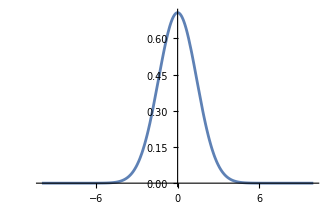

```mathematica
ClearAll[f,g,h,a,b,t,ω]
FourierTransform[f[t],t,ω]
FourierTransform[g[t],t,ω]
FourierTransform[h[t],t,ω]
FourierTransform[a g[t]+b h[t],t,ω]
FourierTransform[D[f[t],t],t,ω]
FourierTransform[f[t,a],t,ω]
f[t_]:=Piecewise[{{t,0<=t<=1},{0,t>1}}];
Complex[FourierTransform[f[t],t,ω]]
FourierTransform[f[t]+g[t]+h[t],t,ω]
FourierTransform[Exp[-t^2],t,ω]
Plot[%,{ω,-10,10}]
```

```mathematica
ClearAll["Global`*"]
f[t_]:=Piecewise[{{Abs[a],Abs[t]<=Abs[a]}}]
Simplify[f[1]]
Simplify[f[a]]
Simplify[f[a/2]]

FourierTransform[f,t,w]
```

Piecewise[{{Abs[a], 1≤Abs[a]}, {0, True}}]

Abs[a]

Abs[a]

f √(2 π) DiracDelta[w]

```mathematica
Simplify[(-(2 Pi M)^(-7/6) M^2)/(2 √(48/(5 Pi)))Alphal/(√l)(f/l)^(-7/6),Assumptions->{l>0}]
```

-(√(5/3) Alphal l^(2/3) M^(5/6))/(16 2^(1/6) f^(7/6) π^(2/3))

```mathematica
25/6-2/3
```

7/2

```mathematica
(5/384)^(1/2)/((√(5/3) Alphal l^(2/3) M^(5/6))/(16 2^(1/6) f^(7/6)))/.{Alphal->1,M->1,f->1,l->1}
```

2^(2/3)

```mathematica
Clear[a,b,B]
asoln=Solve[(a^(1/2)-a^(-1/2))/(a^(1/2)+a^(-1/2))==(1+B)/(1-B) (b^(1/2)-b^(-1/2))/(b^(1/2)+b^(-1/2)),a]
```

{{a→(-b+B)/(-1+b B)}}

```mathematica
a=asoln[[1,1,2]]
```

(-b+B)/(-1+b B)

```mathematica
Series[a,{b,0,10}]
```

-B+(1-B^2) b+(B-B^3) b^2+(B^2-B^4) b^3+(B^3-B^5) b^4+(B^4-B^6) b^5+(B^5-B^7) b^6+(B^6-B^8) b^7+(B^7-B^9) b^8+(B^8-B^10) b^9+(B^9-B^11) b^10+O[b]^11

```mathematica
FullSimplify[(1-c^2)/c /.{c->(1-Sqrt[1-e^2])/e},Assumptions->{Element[e,Reals],0<e<1}]
```

(2 √(1-e^2))/e

```mathematica
FullSimplify[Expand[((1-Sqrt[1-e^2])/e)^2]]
```

-(-2+e^2+2 √(1-e^2))/e^2

```mathematica
FullSimplify[-(4(1-Sqrt[1-e^2])/e Sqrt[1-e^2]/e) +(4(1-e^2)/e^2 s)]
```

-(4 (-1+√(1-e^2)-s+e^2 (1+s)))/e^2

```mathematica
(*Checking Yunes claims!!!*)

f0 = 20
e0 = 0.1
e = 0.01

f = f0 *(e/e0)^(-18/19)
(*Therefore f is roughly 200*)
```

20

0.1

0.01

177.173

```mathematica
f0 = 20
e0 = 0.4
e = 0.01

f = f0 *(e/e0)^(-18/19)
```

20

0.4

0.01

658.826

```mathematica
(*Okay. roughly 1000. that is just multiplication by 4 xD but the rough estimate is multiplied by 5. seems fair enough*)
```

```mathematica
ClearAll["Global`*"]
F = (2 Pi M^(-1/2) (p/(1-e^2))^(3/2))^(-1)
```

(√M)/(2 (p/(1-e^2))^(3/2) π)

```mathematica
psol=p/.Solve[capitalF==(2 Pi M^(-1/2) (p/(1-e^2))^(3/2))^(-1),p,Assumptions->{0<=e<1,0<M,0<capitalF}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

-((-1+e^2) M^(1/3))/(capitalF^(2/3) (2 π)^(2/3))

```mathematica
μsol=μ/.Solve[chirpM==(μ^3 M^2)^(1/5),μ,Assumptions->{Element[{chirpM,M},Reals],0<M,0<=chirpM}][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

chirpM^(5/3)/M^(2/3)

```mathematica
A1=-μsol/(R psol)*M (*Is this equation wrong in Yunes? Is it missing a M? or are the other equations wrong?*)
A2 = - chirpM/R (2 Pi chirpM capitalF)^(2/3)/(1-e^2)

FullSimplify[A1]
FullSimplify[A2]

FullSimplify[A1-A2,Assumptions->{Element[{capitalF,chirpM},Reals],0<=capitalF,0<=chirpM}]
```

(capitalF^(2/3) chirpM^(5/3) (2 π)^(2/3))/((-1+e^2) R)

-(chirpM (capitalF chirpM)^(2/3) (2 π)^(2/3))/((1-e^2) R)

(capitalF^(2/3) chirpM^(5/3) (2 π)^(2/3))/((-1+e^2) R)

(chirpM (capitalF chirpM)^(2/3) (2 π)^(2/3))/((-1+e^2) R)

0

```mathematica
2/5*2/3+2/5
3/5*2/3+3/5
```

2/3

1

```mathematica
O[a]+a
O[a]^2+a
O[a]^2+a^2
O[a]^3+a^2
O[a]^3+a^3
O[a]^3+a^3+a^2+a+a^4
```

O[a]^1

a+O[a]^2

O[a]^2

a^2+O[a]^3

O[a]^3

a+a^2+O[a]^3

```mathematica
ClearAll["Global`*"]
n=2
m=2

y[k_]:=BesselJ[k,k e]

ym =Series[Sum[y[k],{k,1,m}],{e,0,m}]//Normal/.e->e0 + (0.1*e0)^n
Normal[ym]
```

2

2

e/2+e^2/2

e/2+e^2/2

```mathematica
ClearAll["Global`*"]
n=2
m=2

y[k_]:=BesselJ[k,k e]

ym =Series[Sum[y[k],{k,1,m}],{e,0,m}]/.e->e0 + (0.1*e0)^n
Normal[ym]
```

2

2

SeriesData::sdatv: First argument e0+0.01 e0^2 is not a valid variable.

1/2 (e0+0.01 e0^2)+1/2 (e0+0.01 e0^2)^2+O[e0+0.01 e0^2]^3

1/2 (e0+0.01 e0^2)+1/2 (e0+0.01 e0^2)^2+O[e0+0.01 e0^2]^3

```mathematica
ClearAll["Global`*"]
$Assumptions={Element[{b,e,u,s},Reals],0<e<1,0<b<1/e};
b=(1-Sqrt[1-e^2])/e;
eiv=-b+2Sqrt[1-e^2]/e Series[b^s E^(I s u),{s,0,2}];
sinv=FullSimplify[Im[ExpToTrig[eiv]]//Normal,Assumptions->$Assumptions]
ei2v = eiv^2;
sin2v=FullSimplify[Im[ExpToTrig[ei2v]]//Normal,Assumptions->$Assumptions]

cosv=FullSimplify[Re[ExpToTrig[ei2v]]//Normal,Assumptions->$Assumptions]
cos2v=FullSimplify[Re[ExpToTrig[ei2v]]//Normal,Assumptions->$Assumptions]
```

-Im[(√(1-e^2) s (u+ⅈ Log[(1+√(1-e^2))/e]) (-2 ⅈ+s u+ⅈ s Log[(1+√(1-e^2))/e]))/e]

2 Im[1/e^2 s (u+ⅈ Log[(1+√(1-e^2))/e]) (-2 ⅈ (-3+√(1-e^2))+(-5+√(1-e^2)) s u+e^2 (-6 ⅈ+5 s u)+ⅈ (-5+5 e^2+√(1-e^2)) s Log[(1+√(1-e^2))/e])]

-9+1/e^2 2 (5-3 √(1-e^2)+(-5+5 e^2+√(1-e^2)) s^2 u^2-s Log[e/(1+√(1-e^2))] (2 (-3+3 e^2+√(1-e^2))+(-5+5 e^2+√(1-e^2)) s Log[e/(1+√(1-e^2))]))

-9+1/e^2 2 (5-3 √(1-e^2)+(-5+5 e^2+√(1-e^2)) s^2 u^2-s Log[e/(1+√(1-e^2))] (2 (-3+3 e^2+√(1-e^2))+(-5+5 e^2+√(1-e^2)) s Log[e/(1+√(1-e^2))]))

```mathematica
SIN2V = FullSimplify[4Sqrt[1-e^2]/e^2Series[b^s(s Sqrt[1-e^2]-1)E^(I s u),{s,0,2}]//Normal]
```

1/e^2 2 √(1-e^2) (-2+s (2 √(1-e^2)+2 ⅈ (-1+√(1-e^2) s) u+s u^2)-s Log[(1-√(1-e^2))/e] (2-2 √(1-e^2) s+2 ⅈ s u+s Log[(1-√(1-e^2))/e]))

```mathematica
Hy
```